```mathematica
FiveNodes=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];Length[FiveNodes]
```

1024

```mathematica
TableForm[Sort[Tally[Table[With[{g=allGraphs5[k,"graph"]},{EdgeCount[g],Map[Length,RedBlueGreen[k,allGraphs5]]}],{k,FiveNodes}]]],TableDepth->1]
```

{{0,{1,52,0}},1}
{{1,{2,37,14}},10}
{{2,{4,27,22}},45}
{{3,{5,17,31}},10}
{{3,{8,20,25}},110}
{{4,{10,13,30}},70}
{{4,{12,16,25}},15}
{{4,{16,15,22}},125}
{{5,{13,9,31}},30}
{{5,{20,10,23}},150}
{{5,{24,12,17}},60}
{{5,{27,11,15}},12}
{{6,{15,5,33}},5}
{{6,{25,7,21}},15}
{{6,{26,7,20}},120}
{{6,{31,8,14}},60}
{{6,{34,10,9}},10}
{{7,{30,4,19}},20}
{{7,{34,5,14}},60}
{{7,{35,5,13}},10}
{{7,{38,6,9}},30}
{{8,{40,3,10}},30}
{{8,{43,4,6}},15}
{{9,{47,2,4}},10}
{{10,{52,1,0}},1}

```mathematica
SixNodes=Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&];Length[SixNodes]
```

32768

```mathematica
Monitor[TableForm[Sort[Tally[Table[With[{g=allGraphs6[k,"graph"]},{EdgeCount[g],Map[Length,RedBlueGreen[k,allGraphs6]]}],{k,SixNodes}]]],TableDepth->1],k]
```

{{0,{1,203,0}},1}
{{1,{2,151,51}},15}
{{2,{4,114,86}},105}
{{3,{5,77,122}},20}
{{3,{8,87,109}},435}
{{4,{10,60,134}},240}
{{4,{12,70,122}},45}
{{4,{16,67,121}},1080}
{{5,{13,43,148}},90}
{{5,{20,47,137}},1140}
{{5,{24,54,126}},405}
{{5,{27,51,126}},72}
{{5,{32,52,120}},1296}
{{6,{15,26,163}},15}
{{6,{25,34,145}},100}
{{6,{26,34,144}},810}
{{6,{31,38,135}},360}
{{6,{34,45,125}},60}
{{6,{40,37,127}},2160}
{{6,{48,42,114}},1080}
{{6,{54,40,110}},360}
{{6,{58,41,105}},60}
{{7,{30,21,153}},135}
{{7,{34,25,145}},360}
{{7,{35,25,144}},60}
{{7,{38,29,137}},180}
{{7,{50,27,127}},540}
{{7,{52,27,125}},2160}
{{7,{60,30,114}},180}
{{7,{62,30,112}},1800}
{{7,{68,35,101}},300}
{{7,{69,29,106}},360}
{{7,{74,34,96}},180}
{{7,{79,32,93}},180}
{{8,{40,16,148}},180}
{{8,{43,20,141}},90}
{{8,{60,17,127}},360}
{{8,{65,20,119}},360}
{{8,{68,20,116}},1800}
{{8,{70,20,114}},300}
{{8,{76,23,105}},900}
{{8,{80,22,102}},540}
{{8,{81,22,101}},720}
{{8,{83,22,99}},180}
{{8,{87,21,96}},180}
{{8,{89,25,90}},360}
{{8,{94,24,86}},360}
{{8,{96,30,78}},15}
{{8,{98,29,77}},90}
{{9,{47,11,146}},60}
{{9,{75,13,116}},60}
{{9,{80,13,111}},900}
{{9,{86,16,102}},450}
{{9,{89,15,100}},840}
{{9,{92,15,97}},360}
{{9,{95,14,95}},180}
{{9,{97,15,92}},15}
{{9,{99,17,88}},360}
{{9,{101,17,86}},720}
{{9,{102,17,85}},180}
{{9,{105,16,83}},360}
{{9,{108,20,76}},90}
{{9,{111,19,74}},360}
{{9,{114,18,72}},60}
{{9,{128,25,51}},10}
{{10,{52,6,146}},6}
{{10,{94,9,101}},300}
{{10,{105,10,89}},360}
{{10,{107,10,87}},450}
{{10,{110,10,84}},90}
{{10,{114,12,78}},360}
{{10,{116,12,76}},360}
{{10,{118,11,75}},72}
{{10,{119,11,74}},360}
{{10,{121,14,69}},45}
{{10,{124,14,66}},180}
{{10,{126,13,65}},360}
{{10,{136,15,53}},60}
{{11,{104,5,95}},30}
{{11,{125,7,72}},45}
{{11,{126,7,71}},360}
{{11,{128,7,69}},180}
{{11,{136,8,60}},420}
{{11,{142,10,52}},180}
{{11,{145,10,49}},60}
{{11,{146,9,49}},90}
{{12,{141,4,59}},60}
{{12,{150,5,49}},180}
{{12,{153,5,46}},20}
{{12,{158,6,40}},180}
{{12,{163,8,33}},15}
{{13,{168,3,33}},60}
{{13,{175,4,25}},45}
{{14,{188,2,14}},15}
{{15,{203,1,0}},1}

```mathematica
Map[#[[1,2,2]]&,{{{{0,{1,203,0}},1}}, {{{1,{2,151,51}},15}}, {{{2,{4,114,86}},105}}, {{{3,{5,77,122}},20}}, {{{3,{8,87,109}},435}}, {{{4,{10,60,134}},240}}, {{{4,{12,70,122}},45}}, {{{4,{16,67,121}},1080}}, {{{5,{13,43,148}},90}}, {{{5,{20,47,137}},1140}}, {{{5,{24,54,126}},405}}, {{{5,{27,51,126}},72}}, {{{5,{32,52,120}},1296}}, {{{6,{15,26,163}},15}}, {{{6,{25,34,145}},100}}, {{{6,{26,34,144}},810}}, {{{6,{31,38,135}},360}}, {{{6,{34,45,125}},60}}, {{{6,{40,37,127}},2160}}, {{{6,{48,42,114}},1080}}, {{{6,{54,40,110}},360}}, {{{6,{58,41,105}},60}}, {{{7,{30,21,153}},135}}, {{{7,{34,25,145}},360}}, {{{7,{35,25,144}},60}}, {{{7,{38,29,137}},180}}, {{{7,{50,27,127}},540}}, {{{7,{52,27,125}},2160}}, {{{7,{60,30,114}},180}}, {{{7,{62,30,112}},1800}}, {{{7,{68,35,101}},300}}, {{{7,{69,29,106}},360}}, {{{7,{74,34,96}},180}}, {{{7,{79,32,93}},180}}, {{{8,{40,16,148}},180}}, {{{8,{43,20,141}},90}}, {{{8,{60,17,127}},360}}, {{{8,{65,20,119}},360}}, {{{8,{68,20,116}},1800}}, {{{8,{70,20,114}},300}}, {{{8,{76,23,105}},900}}, {{{8,{80,22,102}},540}}, {{{8,{81,22,101}},720}}, {{{8,{83,22,99}},180}}, {{{8,{87,21,96}},180}}, {{{8,{89,25,90}},360}}, {{{8,{94,24,86}},360}}, {{{8,{96,30,78}},15}}, {{{8,{98,29,77}},90}}, {{{9,{47,11,146}},60}}, {{{9,{75,13,116}},60}}, {{{9,{80,13,111}},900}}, {{{9,{86,16,102}},450}}, {{{9,{89,15,100}},840}}, {{{9,{92,15,97}},360}}, {{{9,{95,14,95}},180}}, {{{9,{97,15,92}},15}}, {{{9,{99,17,88}},360}}, {{{9,{101,17,86}},720}}, {{{9,{102,17,85}},180}}, {{{9,{105,16,83}},360}}, {{{9,{108,20,76}},90}}, {{{9,{111,19,74}},360}}, {{{9,{114,18,72}},60}}, {{{9,{128,25,51}},10}}, {{{10,{52,6,146}},6}}, {{{10,{94,9,101}},300}}, {{{10,{105,10,89}},360}}, {{{10,{107,10,87}},450}}, {{{10,{110,10,84}},90}}, {{{10,{114,12,78}},360}}, {{{10,{116,12,76}},360}}, {{{10,{118,11,75}},72}}, {{{10,{119,11,74}},360}}, {{{10,{121,14,69}},45}}, {{{10,{124,14,66}},180}}, {{{10,{126,13,65}},360}}, {{{10,{136,15,53}},60}}, {{{11,{104,5,95}},30}}, {{{11,{125,7,72}},45}}, {{{11,{126,7,71}},360}}, {{{11,{128,7,69}},180}}, {{{11,{136,8,60}},420}}, {{{11,{142,10,52}},180}}, {{{11,{145,10,49}},60}}, {{{11,{146,9,49}},90}}, {{{12,{141,4,59}},60}}, {{{12,{150,5,49}},180}}, {{{12,{153,5,46}},20}}, {{{12,{158,6,40}},180}}, {{{12,{163,8,33}},15}}, {{{13,{168,3,33}},60}}, {{{13,{175,4,25}},45}}, {{{14,{188,2,14}},15}}, {{{15,{203,1,0}},1}}}]
```

{203,151,114,77,87,60,70,67,43,47,54,51,52,26,34,34,38,45,37,42,40,41,21,25,25,29,27,27,30,30,35,29,34,32,16,20,17,20,20,20,23,22,22,22,21,25,24,30,29,11,13,13,16,15,15,14,15,17,17,17,16,20,19,18,25,6,9,10,10,10,12,12,11,11,14,14,13,15,5,7,7,7,8,10,10,9,4,5,5,6,8,3,4,2,1}

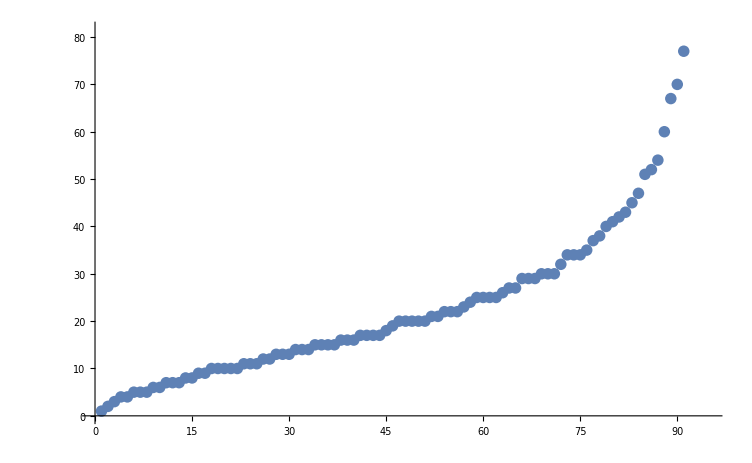

```mathematica
ListPlot[{203,151,114,77,87,60,70,67,43,47,54,51,52,26,34,34,38,45,37,42,40,41,21,25,25,29,27,27,30,30,35,29,34,32,16,20,17,20,20,20,23,22,22,22,21,25,24,30,29,11,13,13,16,15,15,14,15,17,17,17,16,20,19,18,25,6,9,10,10,10,12,12,11,11,14,14,13,15,5,7,7,7,8,10,10,9,4,5,5,6,8,3,4,2,1}//Sort]
```